# Week 10:

## Sunday 19/5:

Q.M Hamiltonians:

Creating the Hamiltonian Hso = Lx ⊗ Sx + Ly ⊗ Sy + Lz ⊗ Sz = L ⊗ S

```mathematica
L[l_]:=Block[{Lxp,Lxm,LX,g,Lyp,Lym,LY,Lzd,LZ},Lxp[a_]:=ℏ/2 √((l+1)(2a)-a (a+1)); Lxm[a_]:=ℏ/2 √((l+1)(2a)-a(a+1));
g=2 l+1; LX=ConstantArray[0,{g,g}];
Lyp[a_]:=-(I ℏ)/2 √((l+1)(2a)-a (a+1)); Lym[a_]:=(I ℏ)/2 √((l+1)(2a)-a(a+1));
LY=ConstantArray[0,{g,g}];Lzd[a_]:=ℏ(l+1-a); LZ=ConstantArray[0,{g,g}];
For[a=1,a<g,a++,LX[[a,a+1]]=Lxp[a];LX[[a+1,a]]=Lxm[a]];For[a=1,a<g,a++,LY[[a,a+1]]=Lyp[a];LY[[a+1,a]]=Lym[a]];For[a=1,a≤g,a++,LZ[[a,a]]=Lzd[a]];
{LX,LY,LZ}]
```

```mathematica
DirectProduct[M1_,M2_]:=ArrayFlatten[Outer[Times,M1,M2]]
```

```mathematica
Hso[l_,s_]:= DirectProduct[L[l][[1]],L[s][[1]]] +DirectProduct[L[l][[2]],L[s][[2]]]+DirectProduct[L[l][[3]],L[s][[3]]]
```

```mathematica
Hso[1/2,1/2]
```

{{ℏ^2/4,0,0,0},{0,-ℏ^2/4,ℏ^2/2,0},{0,ℏ^2/2,-ℏ^2/4,0},{0,0,0,ℏ^2/4}}

```mathematica
H=Hso[1/2,1/2]
id1=IdentityMatrix[2]; id2=IdentityMatrix[2];
X1= DirectProduct[L[1/2][[1]],id2];
Y1=DirectProduct[L[1/2][[2]],id2]; Z1=DirectProduct[L[1/2][[3]],id2];
X2= DirectProduct[id1,L[1/2][[1]]];Y2=DirectProduct[id1,L[1/2][[2]]]; Z2=DirectProduct[id1,L[1/2][[3]]];
```

{{ℏ^2/4,0,0,0},{0,-ℏ^2/4,ℏ^2/2,0},{0,ℏ^2/2,-ℏ^2/4,0},{0,0,0,ℏ^2/4}}

```mathematica
Comm[A_,B_]:=A.B-B.A
```

```mathematica
Comm[H,X1+X2];
Comm[H,Y1+Y2];
Comm[H,Z1+Z2];
Comm[H,H+H+X1.X1+Y1.Y1+Z1.Z1+X2.X2+Y2.Y2+Z2.Z2]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

A nicer way to write J will be:

```mathematica
J={X1+X2,Y1+Y2,Z1+Z2};
Mult1[A_,B_]:= Sum[A[[k]].B[[k]],{k,1,3}]
Jsqured=Mult1[J,J];
Comm[H,Jsqured]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
H2=DirectProduct[L[1/2][[1]],L[1/2][[1]]] + DirectProduct[L[1/2][[2]],L[1/2][[2]]];
```

```mathematica
T1=MatrixExp[-I H t]; T2=MatrixExp[-I H2 t];
up={1,0};
down={0,1};
Kron[v1_,v2_]:=Flatten[Outer[Times,v1,v2]]
ψ=Kron[down,up];
T1.ψ//MatrixForm
T2.ψ//MatrixForm
MatrixForm[H2]
```

(0
1/2 ⅇ^(-1/4 ⅈ t ℏ^2)-1/2 ⅇ^(3/4 ⅈ t ℏ^2)
1/2 ⅇ^(-1/4 ⅈ t ℏ^2)+1/2 ⅇ^(3/4 ⅈ t ℏ^2)
0)

(0
-ⅈ Sin[(t ℏ^2)/2]
Cos[(t ℏ^2)/2]
0)

(0 | 0 | 0 | 0
0 | 0 | ℏ^2/2 | 0
0 | ℏ^2/2 | 0 | 0
0 | 0 | 0 | 0)

## Tuesday 21/5:

Adiabatic Theorem:

For Hamiltonian systems with eigen values e1,e2,...,en if we start the system from a eigen function then it will continue with the same eigen value as long as (d/dt(e2-e1))/(e2-e1)^2<<1 which means the distance between 2 neighboring eigen values (energies) is larger than the change in the eigen value as a function of time
|δ/Ω^2|<<1

{δ-√(1+δ^2),1}

{δ+√(1+δ^2),1}

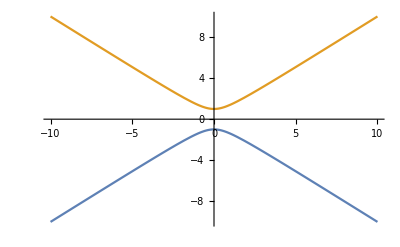

```mathematica
ham={{δ,Ω},{Ω,-δ}};
e1=Eigenvalues[ham][[1]]; e2=Eigenvalues[ham][[2]];
v1=Eigenvectors[ham][[1]]
v2=Eigenvectors[ham][[2]]
Ω=1;
Plot[{e1,e2},{δ,-10,10}]
```

```mathematica
δ=R t;
NDSolve[ham.v1==e2 v1
```

-((0.+0.5 ⅈ) ⅇ^(-1. t √(-1.-0.01 t^2)) (-1.+1. ⅇ^(2. t √(-1.-0.01 t^2))))/(√(-1.-0.01 t^2))+(0.5 ⅇ^(-1. t √(-1.-0.01 t^2)) (1.+1. ⅇ^(2. t √(-1.-0.01 t^2)))-((0.+0.05 ⅈ) ⅇ^(-1. t √(-1.-0.01 t^2)) (-1. t+1. ⅇ^(2. t √(-1.-0.01 t^2)) t))/(√(-1.-0.01 t^2))) (0.1 t-√(1+0.01 t^2))

-Graphics-

```mathematica
up={1,0};
down={0,1};
Kron[v1_,v2_]:=Flatten[Outer[Times,v1,v2]]
```

```mathematica
ND
```